# Motor Characterization Analysis

```mathematica
SetDirectory@NotebookDirectory[];
```

## Load and parse the data

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Import["test results 12-12-2016.txt","Elements"]
```

{Data,Lines,Plaintext,String,Words}

```mathematica
data=Import["test results 12-12-2016.txt","Lines"];
data=Cases[data,Except[""]][[2;;]];
data=Split[data,And[StringContainsQ[#1,"Current"],StringContainsQ[#2,"Current"]]&];
weights=StringSplit[#,"g"][[1]]&/@Flatten@data[[1;;;;2]];
data=data[[2;;;;2]];
parsed=Flatten@MapThread[Map[(result@@Prepend[ToExpression/@(StringSplit[#,","][[2;;;;2]]),weight]&)/.weight->ToExpression@#1,#2]&,{weights,data}];
```

```mathematica
"result[mass,power,current,speed]"
Column@parsed
```

result[mass,power,current,speed]

result[50,25,4.11,55.04]
result[50,38,8.23,132.24]
result[50,0,0.,-56.7]
result[50,10,0.49,0.]
result[50,20,3.04,24.7]
result[50,30,5.78,85.31]
result[50,40,8.85,144.17]
result[50,50,12.31,202.8]
result[50,63,16.81,275.66]
result[50,63,16.9,275.79]
result[50,63,16.67,276.05]
result[50,0,0.,-55.96]
result[50,10,0.54,0.]
result[50,20,3.,26.13]
result[50,30,5.74,86.44]
result[50,40,8.81,145.73]
result[50,50,12.21,202.92]
result[50,60,15.8,259.2]
result[50,69,19.09,310.01]
result[100,0,0.,-116.49]
result[100,10,1.6,-61.62]
result[100,20,3.88,-1.6]
result[100,30,9.05,13.33]
result[100,40,12.79,76.16]
result[100,50,17.25,133.99]
result[100,60,21.86,190.37]
result[100,70,26.69,244.41]
result[100,80,31.17,298.84]
result[100,79,30.21,294.39]
result[150,0,0.,-165.31]
result[150,10,2.63,-126.42]
result[150,20,6.34,-70.49]
result[150,30,10.39,-10.67]
result[150,40,18.84,0.]
result[150,50,23.02,53.94]
result[150,60,28.32,109.34]
result[150,70,33.83,165.97]
result[150,80,40.07,216.6]
result[150,90,46.77,264.4]
result[150,100,54.,310.76]
result[200,10,3.69,-179.84]
result[200,20,8.65,-150.71]
result[200,30,14.25,-102.68]
result[200,40,19.88,-47.09]
result[200,50,28.26,-2.2]
result[200,60,37.19,-0.07]
result[200,70,42.89,60.47]
result[200,80,50.05,115.92]
result[200,90,57.32,166.4]
result[200,100,64.73,210.74]
result[200,110,73.1,248.43]
result[200,120,81.47,284.29]
result[300,30,20.05,-198.09]
result[300,40,28.62,-184.]
result[300,50,38.08,-160.47]
result[300,60,47.,-133.68]
result[300,70,55.88,-95.24]
result[300,80,64.68,0.]
result[300,90,25.29,434.86]

### Convert the data to standard units

```mathematica
final=parsed;
final[[All,1]]=N@UnitConvert[final[[All,1]]*Quantity[, "Grams"]*Quantity[, "StandardAccelerationOfGravity"]*Quantity[2.5, "Centimeters"],"Newton-Meters"];
final[[All,2]]=N@final[[All,2]]/255;
final[[All,3]]=final[[All,3]]*Quantity[5, "Volts"]/1023;
final[[All,4]]=final[[All,4]]/12*Quantity[, ("Revolutions")/("Seconds")];
```

```mathematica
"result[mass,power,current,speed]"
Column@final
```

result[mass,power,current,speed]

result[0.0122583 m N,0.0980392,0.020088 V,4.58667 rev/s]
result[0.0122583 m N,0.14902,0.0402248 V,11.02 rev/s]
result[0.0122583 m N,0.,0. V,-4.725 rev/s]
result[0.0122583 m N,0.0392157,0.00239492 V,0. rev/s]
result[0.0122583 m N,0.0784314,0.0148583 V,2.05833 rev/s]
result[0.0122583 m N,0.117647,0.0282502 V,7.10917 rev/s]
result[0.0122583 m N,0.156863,0.0432551 V,12.0142 rev/s]
result[0.0122583 m N,0.196078,0.0601662 V,16.9 rev/s]
result[0.0122583 m N,0.247059,0.0821603 V,22.9717 rev/s]
result[0.0122583 m N,0.247059,0.0826002 V,22.9825 rev/s]
result[0.0122583 m N,0.247059,0.0814761 V,23.0042 rev/s]
result[0.0122583 m N,0.,0. V,-4.66333 rev/s]
result[0.0122583 m N,0.0392157,0.0026393 V,0. rev/s]
result[0.0122583 m N,0.0784314,0.0146628 V,2.1775 rev/s]
result[0.0122583 m N,0.117647,0.0280547 V,7.20333 rev/s]
result[0.0122583 m N,0.156863,0.0430596 V,12.1442 rev/s]
result[0.0122583 m N,0.196078,0.0596774 V,16.91 rev/s]
result[0.0122583 m N,0.235294,0.0772239 V,21.6 rev/s]
result[0.0122583 m N,0.270588,0.093304 V,25.8342 rev/s]
result[0.0245166 m N,0.,0. V,-9.7075 rev/s]
result[0.0245166 m N,0.0392157,0.00782014 V,-5.135 rev/s]
result[0.0245166 m N,0.0784314,0.0189638 V,-0.133333 rev/s]
result[0.0245166 m N,0.117647,0.0442326 V,1.11083 rev/s]
result[0.0245166 m N,0.156863,0.0625122 V,6.34667 rev/s]
result[0.0245166 m N,0.196078,0.0843109 V,11.1658 rev/s]
result[0.0245166 m N,0.235294,0.106843 V,15.8642 rev/s]
result[0.0245166 m N,0.27451,0.13045 V,20.3675 rev/s]
result[0.0245166 m N,0.313725,0.152346 V,24.9033 rev/s]
result[0.0245166 m N,0.309804,0.147654 V,24.5325 rev/s]
result[0.0367749 m N,0.,0. V,-13.7758 rev/s]
result[0.0367749 m N,0.0392157,0.0128543 V,-10.535 rev/s]
result[0.0367749 m N,0.0784314,0.0309873 V,-5.87417 rev/s]
result[0.0367749 m N,0.117647,0.050782 V,-0.889167 rev/s]
result[0.0367749 m N,0.156863,0.0920821 V,0. rev/s]
result[0.0367749 m N,0.196078,0.112512 V,4.495 rev/s]
result[0.0367749 m N,0.235294,0.138416 V,9.11167 rev/s]
result[0.0367749 m N,0.27451,0.165347 V,13.8308 rev/s]
result[0.0367749 m N,0.313725,0.195846 V,18.05 rev/s]
result[0.0367749 m N,0.352941,0.228592 V,22.0333 rev/s]
result[0.0367749 m N,0.392157,0.26393 V,25.8967 rev/s]
result[0.0490333 m N,0.0392157,0.0180352 V,-14.9867 rev/s]
result[0.0490333 m N,0.0784314,0.0422776 V,-12.5592 rev/s]
result[0.0490333 m N,0.117647,0.0696481 V,-8.55667 rev/s]
result[0.0490333 m N,0.156863,0.0971652 V,-3.92417 rev/s]
result[0.0490333 m N,0.196078,0.138123 V,-0.183333 rev/s]
result[0.0490333 m N,0.235294,0.181769 V,-0.00583333 rev/s]
result[0.0490333 m N,0.27451,0.209629 V,5.03917 rev/s]
result[0.0490333 m N,0.313725,0.244624 V,9.66 rev/s]
result[0.0490333 m N,0.352941,0.280156 V,13.8667 rev/s]
result[0.0490333 m N,0.392157,0.316373 V,17.5617 rev/s]
result[0.0490333 m N,0.431373,0.357283 V,20.7025 rev/s]
result[0.0490333 m N,0.470588,0.398192 V,23.6908 rev/s]
result[0.0735499 m N,0.117647,0.0979961 V,-16.5075 rev/s]
result[0.0735499 m N,0.156863,0.139883 V,-15.3333 rev/s]
result[0.0735499 m N,0.196078,0.186119 V,-13.3725 rev/s]
result[0.0735499 m N,0.235294,0.229717 V,-11.14 rev/s]
result[0.0735499 m N,0.27451,0.273118 V,-7.93667 rev/s]
result[0.0735499 m N,0.313725,0.316129 V,0. rev/s]
result[0.0735499 m N,0.352941,0.123607 V,36.2383 rev/s]

## Plot and analyze the data

```mathematica
weightGroupings=SortBy[#,(#[[2]]&)]&/@GatherBy[final,#[[1]]&];
Column@weightGroupings;
```

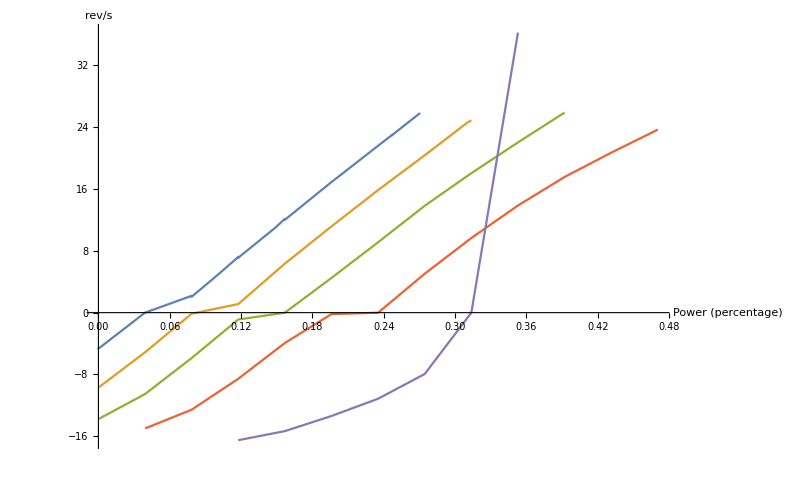

```mathematica
ListLinePlot[({#[[2]],#[[4]]}&/@#)&/@weightGroupings,AxesLabel->{"Power (percentage)",Automatic}]
```